# A Quick Introduction to Mathematica

## Notebooks When you start your Mathematica, go to the menu bar on the RHS and click on File >New>Notebook(.nb), click on the notebook and hit Enter(if it does evaluate hit Shift then Enter)

```mathematica
1+2
```

3

Input cells
Output cells
Group cells
Plain text cells
Title cells
Section cells etc

## Algebraic Maths

Mathematica allows you to do Mathematics just as you would on paper

()  = Bracket
^  = Power
*  = Multiply
/ = Divide
+  = Add
-  = Subtract

```mathematica
2(x+1)
```

2 (1+x)

```mathematica
x^2
```

x^2

```mathematica
x*x
```

x^2

## Assignment

You can assign values or expressions to variables using =

```mathematica
y = x^2
```

x^2

```mathematica
y1 = x*x+ 3
```

3+x^2

```mathematica
y2 = y1*y
```

x^2 (3+x^2)

```mathematica
y3 =  x/y
```

1/x

## Set Delayed : = Delayed Assignment

```mathematica
x1 =2
```

2

```mathematica
y := x1* x1(*It is not evaluated*)
```

I can change the value of x1 at any point

```mathematica
y
```

4

```mathematica
x1 =3
```

3

```mathematica
y
```

9

## Numerical evaluation

```mathematica
20/3
```

20/3

Include and N to get decimals

```mathematica
N[20/3]
```

6.66667

choose the decimal places

```mathematica
N[20/3,10]
```

6.666666667

```mathematica
20/3 //N
```

6.66667

#### Another way to achieve this is define a pure function

def  func (x) :
 return x**2

```mathematica
yy[x_]:= x^2
```

```mathematica
yy[2]
```

4

```mathematica
yy[3]
```

9

```mathematica
yy[4]
```

16

### Replacement Operator

```mathematica
x*x/.x->2
```

4

```mathematica
->
```

4

replace /. = such that x->2 goes to 2

```mathematica
Mass = Density* Volume/.{Density-> ρ,Volume->(4/3) π r^3}
```

4/3 π r^3 ρ

## Single variable vs mathematical operations

```mathematica
A*B
```

A B

is the same thing as

```mathematica
A B
```

A B

For numbers, a cross is inserted automatically

```mathematica
2 3
```

6

However, this is a single variable

```mathematica
AB
```

AB

2 space (times) A

```mathematica
2 A
```

2 A

### Suppressing Output

```mathematica
x = 42;
```

Put a semicolon at the end of the assignment to stop output being created.

### Clearing variables

Remove any variable definition

```mathematica
Clear[y,  yy]
```

```mathematica
x
```

42

```mathematica
x =.
```

```mathematica
x
```

x

### History

%  The last output
%% The last but one output

%%% The last but two output

Out[13]
In[1]

```mathematica
Out[21]
```

x

## Lists

A list in Mathematica is a collection of objects that can be used to form a vector, a matrix or an array

```mathematica
x={2,3,4,5,5}
```

{2,3,4,5,5}

For a two dimensional array, use

```mathematica
A= {{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
A//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
B={{1,2,3},{4,5,6},{4,2,3}}
```

{{1,2,3},{4,5,6},{4,2,3}}

```mathematica
B//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
4 | 2 | 3)

N-dimensional array is  a list of lists

## Built-n Functions

Mathematica has hundreds of built-in functions

```mathematica
Sin[x1]
Exp[x1]
Eigenvalues[A]//N
Eigenvectors[A]
```

Sin[3]

ⅇ^3

{5.37228,-0.372281}

## Postfix functions

```mathematica
Clear[x]
```

```mathematica
Expand[(1+x)^2]
Simplify[a(1+1/a)]
Collect[x^2 + 5 x +6 + x + 3 x^2,x]
```

1+2 x+x^2

1+a

6+6 x+4 x^2

Or

```mathematica
(1+x)^2//Expand
a(1+1/a)//Expand
```

1+2 x+x^2

1+a

### Help

Mathematica Documentation center

Help > Documentation center

### Palettes

### Basic Math Assistant Palette

### Place holders

### Special Characters

Using Palettes can be very tedious, that’s why there are short cuts

There are many short  cuts, to find more place the pointer over a button on a pallet, it will show the equivalent key sequences to the button.

### Special Numbers, Characters and Symbols

### For Greek letters

```mathematica
β
```

### Pictogram key sequences

Esc < == > Esc

```mathematica
⟺
```

Syntax::sntxi: Incomplete expression; more input is needed .

Esc : Esc

```mathematica
:>
```

τ

```mathematica
☺
```

### Natural Language processing

WolframAlphaQueryParseResults

2.65085×10^12 $

WolframAlphaQueryParseResults

x-x^3/6+x^5/120+O[x]^6

WolframAlphaQueryParseResults

10000. $

Wolfram

WolframAlphaQueryResults

Add ctrl + = converts the natural language to Mathematica input. Eg Type power series of cos(x)

```mathematica
LinguisticAssistant
```

1-x^2/2+x^4/24+O[x]^6

## Lists and Matrix operation

### Operating on lists

```mathematica
Clear[A,B]
```

```mathematica
A = {a1,a2,a3}
B= {b1,b2,b3}
```

{a1,a2,a3}

{b1,b2,b3}

```mathematica
A+B
```

{a1+b1,a2+b2,a3+b3}

```mathematica
A-B
```

{a1-b1,a2-b2,a3-b3}

```mathematica
A*B
```

{a1 b1,a2 b2,a3 b3}

```mathematica
A/B
```

{a1/b1,a2/b2,a3/b3}

```mathematica
A^B
```

{a1^b1,a2^b2,a3^b3}

```mathematica
A.B
```

a1 b1+a2 b2+a3 b3

```mathematica
A  × B
```

{-a3 b2+a2 b3,a3 b1-a1 b3,-a2 b1+a1 b2}

### Operations on Matrices

Normal operations like +- operate on elements by a corresponding element, Matrix multiplication is achieved by A.B

### Indexing vectors

```mathematica
x = {10,11,12,13,14,15}
```

{10,11,12,13,14,15}

```mathematica
x⟦3⟧
```

12

There are many commands that operate on matrics, to get more insights on what is available open Basic Math Assistant palette and click on MatricxCommands,

### Generating Lists

Range: produces a vector containing a specified range of numbers

Range[n(int)]

```mathematica
Range[5]
```

{1,2,3,4,5}

Range[n(start), m(end)]

```mathematica
Range[3,7]
```

{3,4,5,6,7}

Range[n(start), m(end), s(spacing)]

```mathematica
Range[3,7,2]
```

{3,5,7}

Table:it applies an expression to a range of inputs

```mathematica
Table[n!,{n,5}]
```

{1,2,6,24,120}

```mathematica
Table[x^2,{x,0,4}]
```

{0,1,4,9,16}

```mathematica
Table[x^2,{x,{1,4,8}}]
```

{1,16,64}

```mathematica
Table[{x,x^2},{x,0,4}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16}}

The above example is a matrix, you can visualize as

```mathematica
Table[{x,x^2},{x,0,4}]//TableForm
```

0 | 0
1 | 1
2 | 4
3 | 9
4 | 16

Grid is a function that can be used to frame a table

```mathematica
Grid[Table[{x,Sin[x]},{x,0,π,π/3}]]
```

0 | 0
π/3 | (√3)/2
(2 π)/3 | (√3)/2
π | 0

### Algebraic Manipulate

Simplify: simplifies an expression

```mathematica
Simplify[(x^3 + 6 x^2 + 11 x + 6)/(x^2 + 4 x + 3)]
```

2+x

```mathematica
Simplify[(Exp[x] + Exp[-x])/2]
```

1/2 (ⅇ^-x+ⅇ^x)

Use full simplify to simplify even further

```mathematica
FullSimplify[(Exp[x] + Exp[-x])/2]
```

Cosh[x]

Expand  Expand out the bracket

```mathematica
Expand[(1+x)(x+2)]
```

2+3 x+x^2

Factor:

```mathematica
Factor[2+3*x+x^2]
```

(1+x) (2+x)

Apart:  Split into partial fractions

```mathematica
Apart[x/(x^2 + 3 x+ 2)]
```

-1/(1+x)+2/(2+x)

Together: Use together to put them under one denominator

```mathematica
Together[-(1+x)^(-1)+2/(2+x)]
```

x/((1+x) (2+x))

Cancel: Cancel common factors in the Numerator and the denominator

```mathematica
Cancel[(x^2-1)/(x-1)]
```

1+x

TrigExpand and TrigFactor are specifically for trigonometric functions. TrigToExp converts trigonometric functions to there exponential equivalent. ExpToTrig the reverse of the above.
ExpandNumerator, ExpandDenominator, FunctionExpand and PowerExpand. Then there is the more general function ExpandAll.

```mathematica
?TrigExpand
```

TrigExpand[expr] expands out trigonometric functions in expr.

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

```mathematica
?TrigFactor
```

TrigFactor[expr] factors trigonometric functions in expr.

```mathematica
TrigFactor[Sin[x]^2+Tan[x]^2]
```

1/2 (3+Cos[2 x]) Tan[x]^2

```mathematica
?TrigToExp
```

TrigToExp[expr] converts trigonometric functions in expr to exponentials.

```mathematica
TrigToExp[Cos[x]]
```

ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2

```mathematica
?ExpToTrig
```

ExpToTrig[expr] converts exponentials in expr to trigonometric functions.

```mathematica
ExpToTrig[Exp[I x]]
```

Cos[x]+ⅈ Sin[x]

```mathematica
?ExpandNumerator
```

ExpandNumerator[expr] expands out products and powers that appear in the numerator of expr.

```mathematica
ExpandNumerator[(x-1)(x-2)/((x-3)(x-4))]
```

(2-3 x+x^2)/((-4+x) (-3+x))

```mathematica
?ExpandDenominator
```

ExpandDenominator[expr] expands out products and powers that appear as denominators in expr.

```mathematica
ExpandDenominator[(x-1)(x-2)/((x-3)(x-4))]
```

((-2+x) (-1+x))/(12-7 x+x^2)

```mathematica
ExpandDenominator[1/(x+1)+2/(x+1)^2+3/(x+1)^3]
```

1/(1+x)+2/(1+2 x+x^2)+3/(1+3 x+3 x^2+x^3)

```mathematica
?FunctionExpand
```

FunctionExpand[expr] tries to expand out special and certain other functions in expr, when possible reducing compound arguments to simpler ones. 
FunctionExpand[expr,assum] expands using assumptions.

```mathematica
FunctionExpand[Sin[24Degree]]
```

-1/8 √3 (-1-√5)-1/4 √(1/2 (5-√5))

```mathematica
FunctionExpand[ChebyshevT[n,x]]
```

Cos[n ArcCos[x]]

```mathematica
FunctionExpand[HypergeometricPFQ[{1/2},{1,1},z]]
```

BesselI[0,√z]^2

```mathematica
?PowerExpand
```

PowerExpand[expr] expands all powers of products and powers. 
PowerExpand[expr,{x_1,x_2,…}] expands only with respect to the variables x_i.

```mathematica
PowerExpand[Sqrt[x y]]
```

√x √y

```mathematica
PowerExpand[Sqrt[x y],Assumptions->True]
```

ⅇ^(ⅈ π Floor[1/2-Arg[x]/(2 π)-Arg[y]/(2 π)]) √x √y

```mathematica
ExpandAll[Sqrt[x y]]
```

√(x y)

### Functions for extracting part of an expression

Exponent[y,x] :Largest exponent of x in y

```mathematica
Exponent[x^3+6x^2+11x+6,x]
```

3

Part[y,n] The nth term of y.

```mathematica
Part[x^3+6x^2+11x+6,1]
Part[x^3+6x^2+11x+6,2]
Part[x^3+6x^2+11x+6,3]
```

6

11 x

6 x^2

Coefficient[y,x] The coefficient of x in y

```mathematica
Coefficient[x^3+6x^2+11x+6,x]
Coefficient[x^3+6x^2+11x+6,x^2]
Coefficient[x^3+6x^2+11x+6,x^3]
```

11

6

1

CoefficientList: Put all the coefficients of x into a list

```mathematica
Numerator[(x^3+6x^2+11x+6)/(x^2 + 4 x + 3)]
```

6+11 x+6 x^2+x^3

```mathematica
Denominator[(x^3+6x^2+11x+6)/(x^2 + 4 x + 3)]
```

3+4 x+x^2

### Solvers

Solve

```mathematica
R=Solve[x^3-6x^2+11x-6==0,x]
```

{{x→1},{x→2},{x→3}}

```mathematica
x1 = x/.First[R]
x2 = x/.R[[2]]
x3 = x/.Last[R]
```

1

2

3

```mathematica
xall = x/.R
```

{1,2,3}

Solve can solve a system of equations

```mathematica
R=Solve[x^2+y^2==2&&x-y==0,{x,y}]
```

{{x→-1,y→-1},{x→1,y→1}}

You can also include inequalities, you can restrict the above to just the positive solution.

```mathematica
R=Solve[x^2+y^2==2&&x-y==0&&x>0,{x,y}]
```

{{x→1,y→1}}

Sometime complex solutions are not appropriate. In the example below the solutions domain has been restricted to real numbers by specifying the domain in a third argument.

```mathematica
Solve[x3==8,x,Reals]
```

{}

Numerical solution is also possible

```mathematica
NSolve[Cos[x]==x,x,Reals]
```

{{x→0.739085}}

### Calculus

Differentiation

Integration

### Solving Differential equations

The function DSolve is used to solve differential equations.

```mathematica
DSolve[y''[x]+2y'[x]+2y[x]==0,y[x],x]
```

{{y[x]→ⅇ^-x C[2] Cos[x]+ⅇ^-x C[1] Sin[x]}}

The first argument can be a list of equations. For example, we could include the initial conditions.

```mathematica
DSolve[{y''[x]+2y'[x]+2y[x] == 0,y[0] == 0,y'[0] == 1},y[x],x]
```

{{y[x]→ⅇ^-x Sin[x]}}

If you cannot solve the equation symbolically, you can try a numerical solution.

```mathematica
A=NDSolve[{y''[x]+2y'[x]+2y[x] ==0,y[0]==0,y'[0]==1},y[x],{x,0,2π}]
```

{{y[x]→InterpolatingFunction[…][x]}}

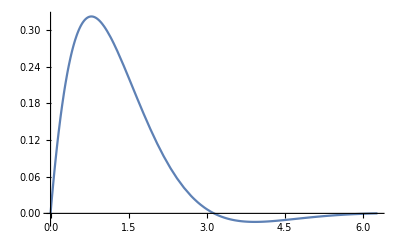

```mathematica
Plot[y[x]/.A[[1]],{x,0,2π}]
```

## Summation

```mathematica
Sum[x^n,{n,1,∞}]
```

-x/(-1+x)

```mathematica
Sum[n,{n,1,2x-1,2}]
```

Floor[x]^2

Limits

```mathematica
Limit[Sin[x]/x,x -> 0]
```

1

## Plot

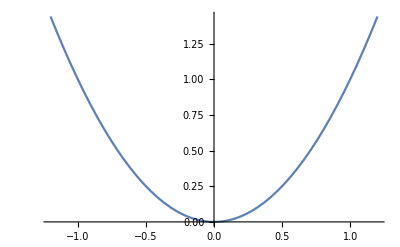

```mathematica
Plot[x^2,{x,-1.2,1.2}]
```

You can plot several lines at once by using a list of expressions.

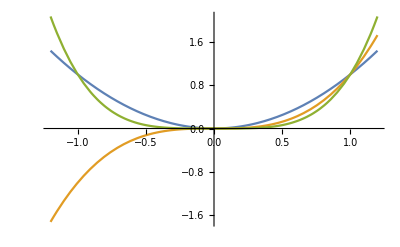

```mathematica
Plot[{x^2,x^3,x^4},{x,-1.2,1.2}]
```

Parametric Plot: A parametric plot uses two expressions. One expression is used for the X coordinate, the other expression for the Y coordinate.

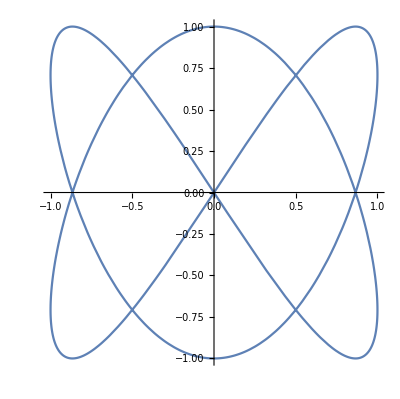

```mathematica
ParametricPlot[{Sin[2q],Cos[3q]},{q,0,2π}]
```

ListPlot: This is used to plot individual points onto a graph. The argument is a list of x,y coordinates.

```mathematica
ListPlot[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}]
```

{{-4,16},{-3,9},{-2,4},{-1,1},{0,0},{1,1},{2,4},{3,9},{4,16}}

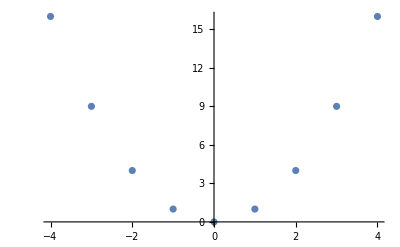

```mathematica
Tz=Table[{x,x^2},{x,-4,4,1}]
ListPlot[Tz]
```

```mathematica
ListLinePlot
ListLogPlot
ListLogLinearPlot 
ListLogLogPlot
```

```mathematica
?Plot
```

System`Plot

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

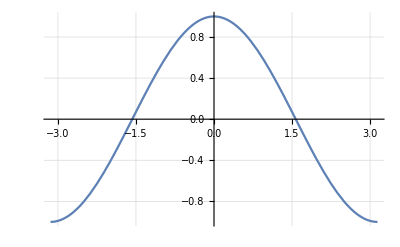

```mathematica
Plot[Cos[x],{x,-π,π},GridLines->Automatic]
```

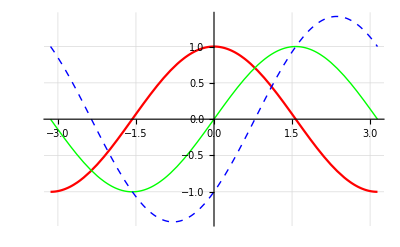

```mathematica
Plot[{Cos[x],Sin[x],Sin[x]-Cos[x]},{x,-π,π},GridLines->Automatic,PlotStyle->{Red,{Green,Thick},{Blue,Dashed,Thin}}]
```

```mathematica
RGBColor[0.9,1,0.9]
RGBColor[0.9,0.5,0.9]
RGBColor[0.2,1,0.9]
RGBColor[0.9,1,0.2]
```

RGBColor[0.9, 1, 0.9]

RGBColor[0.9, 0.5, 0.9]

RGBColor[0.2, 1, 0.9]

RGBColor[0.9, 1, 0.2]

### Style

```mathematica
Style[B=Sqrt[1/(1+w^(2n))],32,Bold]
```

√(1/(1+w^(2 n)))

```mathematica
Style[Hello World,64,Red,Italic,FontFamily ->"Impact"]
```

Hello World

### Combining Multiple Graphs

```mathematica
G1=ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2 Pi}];
G2=ListPlot[{{−1/2,−√3/2},{−1/2,√3/2}},PlotMarkers->Style["×",Red,16]];
```

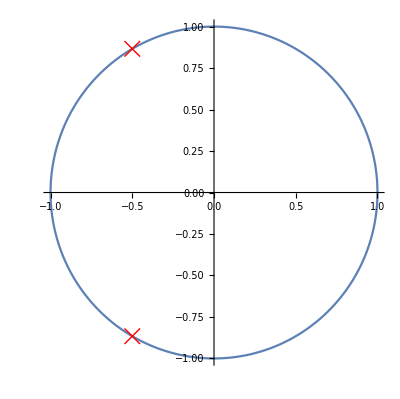

```mathematica
Show[G1,G2]
```

### Defining your own functions

### Compound Expression

A compound expression is a sequence of expressions

```mathematica
c=x=a;y=b;x+y
```

```mathematica
c[a_,b_]:=(x=a;y=b;x+y)
```

```mathematica
c[2,3]
```

5

### Module

Anything being stored in x will be overwritten every time the function is used.

```mathematica
c[a_,b_]:=Module[{x,y},x=a;y=b;x+y]
```

```mathematica
c[4,3]
```

7

### Flow Control

### Interactive Graphs

```mathematica
Manipulate[Plot[Sin[2 π f t],{t,0,1}],{f,1,5}]
```